## code Archived (Principle Directions/EigenVectors)

```mathematica
(* Clear@findSym;
findSym[mask_,option_:False]:=Block[{imd,nx,ny,points,weights,mass,centerOfMass,pointsCom,diag,inertia,v1,v2},
imd=Transpose@ImageData[mask];(* here we transpose the image data *)
{nx,ny}=Dimensions[imd];(* dimensions of the image *)
points=Tuples[{Range[nx],Reverse@Range[ny]}]; (* x-y coordinates on the image *)
weights=Flatten[imd]; (* vector of imagedata *)

centerOfMass=ImageMeasurements[mask,"IntensityCentroid"];(* here we calculate the x-y coordinate of the center of mass *)

pointsCom=(Subtract[#,centerOfMass]&/@points) weights; (* we subtract from each point the center of mass. This gives us a vector of n number of points the {x,y} coordinates of which are displacements from the centroids. We multiply this resulting matrix with the intensity vector. This gives us a vector consisting of two coordinates which are x y displacments from centroid * intensity for each point in the grid *)

diag=Total[(#.#)&/@pointsCom]; (* sum of the {x,y}.{x,y} from above. gives a single values *)
inertia=Table[KroneckerDelta[i,j] diag-Total[(#[[i]] #[[j]])&/@pointsCom],{i,2},{j,2}]; (* inertia *)

{v1,v2}=Eigenvectors[inertia]; (* extracting eigenvectors from inertia *)
(* Print["center of Mass: ", centerOfMass,"\n","pt1 : ",v1 + centerOfMass,"\n","pt2 : ",v2 + centerOfMass]; *)

(* display *)
If[option,Print@Show[mask,Graphics[{{Thick,Dashed,XYZColor[0,0,1,0.6],InfiniteLine[{v2+centerOfMass,centerOfMass}]},{Thick,Dashed,XYZColor[1,0,0,0.6],InfiniteLine[{v1+centerOfMass,centerOfMass}]},{Darker@XYZColor[0,1,0,0.5],PointSize[Large],Point[centerOfMass]},Red,Point[v1+centerOfMass],Blue,Point[v2+centerOfMass]}]]];
{centerOfMass,v1,v2}
] *)
```

```mathematica
(* Clear@maskToRegion;
maskToRegion[mask_]:= Block[{pixelvaluepos,tour,pixelposordered},
pixelvaluepos= PixelValuePositions[MorphologicalPerimeter@mask,1];
tour=Last@FindShortestTour[pixelvaluepos];
pixelposordered = Part[pixelvaluepos,tour];
{pixelposordered,BoundaryMeshRegion[N@pixelvaluepos,Line@tour]}
] *)
```

```mathematica
(* Clear@bisectMask;
bisectMask[mask_,option_:False]:= Block[{centerofMass,v1,v2,pixelordered,ℛ1,ℛ2,temp,pt1,pt2,list,
trimList,npixelordered,nf, ptslocation,firstPreMask,secondPreMask,dim},
dim=First@ImageDimensions[mask];
{centerofMass,v1,v2}=findSym[mask];
{pixelordered,ℛ1}=maskToRegion[mask];
ℛ2=InfiniteLine[{centerofMass,centerofMass+v1}];
list=(RegionIntersection[ℛ2,#]&/@MeshPrimitives[ℛ1,1]//Cases[#,Point[arg_]:> arg]&);

trimList[ls_]:= Module[{p=ls,pairs,firstelem = First@ls,dist,maxdist},
pairs={firstelem,#}&/@p;
dist=EuclideanDistance[##]&@@@pairs;
maxdist=Max@dist;
pairs[[First@@Position[dist,maxdist]]]
]/;Length@ls>2;

{pt1,pt2}=trimList[list]/.trimList[arg__]:> arg;

If[option,temp=Show[HighlightMesh[ℛ1,{Style[1,Directive[XYZColor[0,0,1,0.9]]],Style[2,Directive[XYZColor[0,0,1,0.18]]]}],Graphics[{Red,PointSize[Large],Point@pt1,PointSize[Large],Darker@Green,
Point@pt2,Thick,Dashed,XYZColor[1,0,0,0.5],ℛ2,Blue,Point@centerofMass}]
]
];

npixelordered = N@pixelordered;
nf=Nearest[npixelordered];
ptslocation=Flatten@Position[npixelordered,Flatten@nf[pt1]|Flatten@nf[pt2]];

firstPreMask=PadRight[#,Length@#+1,#]&@Part[pixelordered,First@ptslocation;;Last@ptslocation]//Graphics[{White,Line@#},PlotRange->{{0,dim},{0,dim}}]&//Rasterize[#,"Image",Background->Black,ImageSize->{{dim},{dim}}]&//FillingTransform@*Binarize;

secondPreMask=Join[pixelordered[[;;First@ptslocation+1]],pixelordered[[Last@ptslocation+1;;]]]//Graphics[{White,Line@#},PlotRange->{{0,dim},{0,dim}}]&//Rasterize[#,"Image",Background->Black,ImageSize->{{dim},{dim}}]&//FillingTransform@*Binarize;

Switch[option,True,Join[{temp},{centerofMass},pt1,pt2],_,Join[{centerofMass},pt1,pt2]]
]
*)
```

## Initialize

```mathematica
<<"C:\\Users\\aliha\\Desktop\\analysis notebooks\\96 hours\\principleDir.m"
```

## 1. Mean Intensity of E-Cadherin

```mathematica
(*  contrast, elongation and fourier elliptic descriptors  *)
```

```mathematica
img=ImageAdjust@Import@"C:\\Users\\aliha\\Desktop\\research related\\raw data\\@96 hours\\chi pos\\2\\img_000000000_Empty_000.tif";
ecad = ImageAdjust@Import@"C:\\Users\\aliha\\Desktop\\research related\\raw data\\@96 hours\\chi pos\\2\\imagecorrMinusMean2.tiff";
mask =Import@"C:\\Users\\aliha\\Desktop\\research related\\raw data\\@96 hours\\chi pos\\2\\Mask.tif";
```

```mathematica
HighlightImage[ecad,mask,ImageSize->Medium]
```

-Graphics-

```mathematica
pixpos=PixelValuePositions[ImageCrop@Binarize[ecad*mask],1];
```

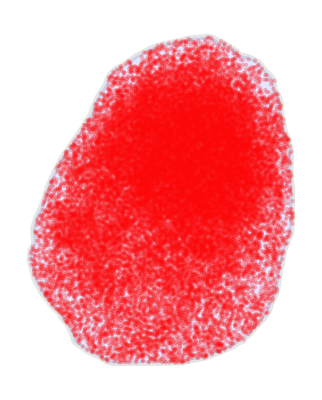

```mathematica
superposed=Show[HighlightMesh[ImageMesh[ImageCrop@mask,Method->"LinearSeparable"],{Style[2,Blue,Opacity[0.1]],
Style[1,Black,Thickness[0.01]]}],Graphics[{Opacity[0.25],Red,Point@pixpos}]]
```

```mathematica
HighlightImage[img,mask,ImageSize->Medium]
```

-Graphics-

## Contrast of E-Cadherin along pseudo-axes of symmetry

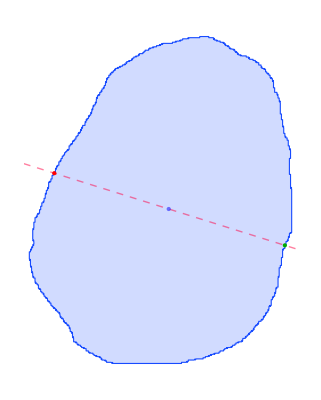
{-Graphics-,{123.738,136.601},{23.,168.028},{226.,104.698}}

```mathematica
{symmb,centroid,pt1,pt2}=bisectMask[ImageCrop[mask],True]
```

## 4. r(θ) and contrast(θ)

```mathematica
boundary=PixelValuePositions[ImageCrop[MorphologicalPerimeter@mask],1];
tour=Last@FindShortestTour[boundary];
boundaryc=Part[boundary,tour];
nF=Nearest[boundaryc];
```

```mathematica
ℛ1=BoundaryMeshRegion[boundary,Line@tour];
```

```mathematica
ℛ2=InfiniteLine[{centroid,pt1}];
```

```mathematica
intersections=Cases[RegionIntersection[ℛ2,#]&/@MeshPrimitives[ℛ1,1],_Point]/.Point[{x_}]:> x;
```

```mathematica
div=5;
```

```mathematica
rotationTransform=RotationTransform[div Degree,centroid]
```

TransformationFunction[(0.996195 | -0.0871557 | 12.3764
0.0871557 | 0.996195 | -10.2647
0. | 0. | 1.)]

```mathematica
pts=Rest@NestList[rotationTransform,pt1,360/div];
```

```mathematica
arrow=Arrow[{centroid,#}]&/@pts;
```

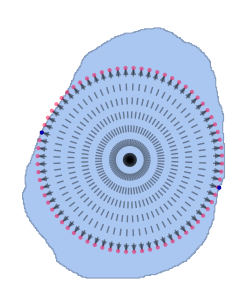

```mathematica
Show[ℛ1,Graphics[{{Arrowheads-> Small,Thick,Dashed,XYZColor[0,0,0,0.4],arrow},
{XYZColor[1,0,0,0.5],PointSize[Medium],Point@pts},{Darker@Blue,PointSize[Large],Point@intersections}
}]]
```

```mathematica
infinitelines=InfiniteLine[{centroid,#}]&/@pts;
```

```mathematica
boundary=PixelValuePositions[ImageCrop[MorphologicalPerimeter@mask],1];
tour=Last@FindShortestTour[boundary];
boundaryc=Part[boundary,tour];
```

```mathematica
contour = Polygon@boundaryc;
(*surfacepts=(x↦RegionIntersection[x,contour])/@infinitelines/.Point[x_]:>x; *)
```

```mathematica
surfacepts=Graphics`Mesh`FindIntersections[Graphics[{FaceForm[],EdgeForm[Blue],contour,#}]]&/@infinitelines;
```

```mathematica
pos=Position[surfacepts,_?(Length@#>2&),{1}];
```

```mathematica
surfacepts2=MapAt[Sequence@@TakeLargestBy[Permutations[#,{2}],EuclideanDistance[#[[1]],#[[2]]]&,1]&,surfacepts,pos];
```

```mathematica
surfacepts3=Part[surfacepts2,All;;Length[surfacepts2]/2];
```

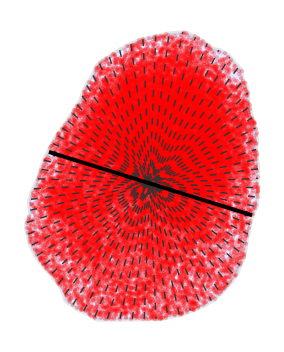

```mathematica
Show[superposed,Graphics[{{Dashed,GrayLevel[0.2],Thick,Line@surfacepts3},{Thickness[0.01],Black,Arrowheads[{-.05,.05}],Arrow@{pt1,pt2}}}]]
```